```mathematica
m l D[D[θ,t],t]+γ D[θ,t]+W Sin[θ]==A Cos[ω t]
```

W Sin[θ]==A Cos[t ω]

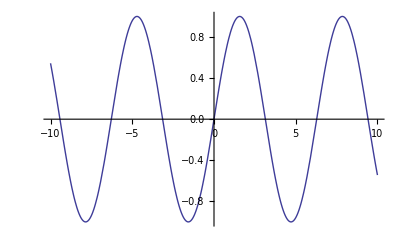

```mathematica
Plot[Sin[x],{x,-10,10}]
```

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f.

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
m l D[D[θ,t],t]+γ D[θ,t]+W Sin[θ]==A Cos[ω t]
```

W Sin[θ]==A Cos[t ω]

```mathematica
(* The goal now is to find the viable ranges for each of these variables.  θ most likely goes from 0 to 2π, but for the others, there's no knowing without knowing what they represent.  (t), which is the independent variable, starts at 0 and counts upward.  The others: (m, l, γ W ω and A) are all parameters. and some of these are pretty straightforward: m = mass, l = length, A is the amplitude of the oscilations, ω is the angular frequency of oscillations, and presumably therefore, γ has something to do with the coefficient of friction at the pivot, and W has something to do with gravity? *)
```

```mathematica
Manipulate[m l D[D[θ,t],t]+γ D[θ,t]+W Sin[θ]==A Cos[ω  t],{m,0,2},{l,},{γ,0,1},{W,0,10},{A,0,1},{ω, 0,5}]
```